```mathematica
Constants
```

```mathematica
(* Physical constants in SI units*)
NAvogadro=6.022140857×10^23;
elcharge=1.6021766208×10^-19; (* Elementary charge in C *)
kB=1.38066×10^-23; (* Boltzmann's constant in J K-1 *)
ε0=8.8541878×10^-12; (* Permittivity of free space in C V-1 m-1 *)
n=1.33; (* Optical refractive index of water *)
n0solv=3.33679×10^28; (* Number of water molecules per m3  *) 
R=8.3144598`10; (* Gas constant *)

au2kcal=627.5095`10;

(*Physical constants in au:*)
hbar=1;
hbarps=0.047685388`10/(au2kcal*π);
Dalton=1822.8900409014022`15;
MassH=1.0072756064562605`15;
MassD=2.0135514936645316`15;
MassT=3.0160492`15;
mH=MassH*Dalton;
mD=MassD*Dalton;
mT=MassT*Dalton;
kb=3.16683`10*10^-6;
 
(* Relative permittivity of water *)
εw=78.49; (* for bulk water *)
εCL=2.0; (* in contact layer *) 

(* Faraday's constant: C mol-1 *)
F=96485.33289`10;
```

## Conversion factors

```mathematica
a2m=10^-10;
m2a=10^10;
e2coul=elcharge;
coul2e=1/e2coul;
bohr2a=0.529177`10;
a2bohr=1/bohr2a;
au2kcal=627.5095`10;
kcal2au=1/au2kcal;
ev2cm=8065.54477`10;
cm2ev = 1/ev2cm ;
au2ev=27.2113`10 ;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
ev2kcal=ev2au*au2kcal;
kcal2ev=1/ev2kcal;
au2ps=2.4189`10*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
kg2amu=1.660539`10*10^-27;
J2ev=6.2415*10^18;
ev2J=1/J2ev;
kcal2J=4184;
J2kcal=1/kcal2J;
```

## 1D Morse Potentials

```mathematica
(*
Construction of gas phase adiabatic PES for each k-product state along proton coordinate; 0 denotes infinite separation
*)

(*
DE1 - dissociation energy (kcal/mol);
DE2 - dissociation energy (kcal/mol);
Beta1 - beta parameter (1/Bohr);
Beta2 - beta parameter (1/Bohr);
W - coupling parameter between reactor and product diabatic states, in kcal/mol;
Δ - Subscript[ϵ, D]+Subscript[J, DD]-Subscript[ϵ, l], in kcal/mol;
R - distance between donor and acceptor, in Å;
rp - distance from minima of left PES, in Å.
*)


(*
Calculation of Morse beta parameter from vibrational frequency and dissociation energy
*)

(*
ω - vibrational frequency in cm-1;
DE - dissociation energy in kcal mol-1;
μ - reduced mass in amu;
Returns Morse beta parameter in bohr-1
*)

BetaMorse[ω_,DE_,μ_]:=ω cm2au√(μ/(2(DE/au2kcal)));


(*
Construction of gas phase diabatic PES for each k-product state along proton coordinate; 0 denotes infinite separation
*)

(*
DE1 - dissociation energy (kcal/mol);
DE2 - dissociation energy (kcal/mol);
Beta1 - beta parameter (1/Bohr);
Beta2 - beta parameter (1/Bohr);
W - coupling parameter between reactor and product diabatic states, in kcal/mol;
Δ - Subscript[ϵ, D]+Subscript[J, DD]-Subscript[ϵ, l], in kcal/mol;
R - distance between donor and acceptor, in Å;
rp - distance from minima of left PES, in Å.
*)

(*
Morse potential energy curve for donor
*)

MorseLeft[Beta_,DE_,rp_,rDH_]:=Module[{r},
	r=a2bohr*(rp-rDH);
	DE(Exp[-2*Beta*r]-2Exp[-Beta*r])
];

(*
Morse potential energy curve for acceptor
*)

MorseRight[Beta_,DE_,rp_,rAH_,R_]:=Module[{r},
	r=-1*a2bohr*(rp-R+rAH);
	DE(Exp[-2*Beta*r]-2Exp[-Beta*r])
];

(*
Gas-phase Adiabatic PES: ground state
*)

AdGS[DE1_,Beta1_,DE2_,Beta2_,rDH_,rAH_,W_,Δ_,R_,rp_,offset_]:=Module[{U1,U2},
U1=MorseLeft[Beta1,DE1,rp,rDH];
U2=MorseRight[Beta2,DE2,rp,rAH,R]+Δ;
N[(U1+U2-Sqrt[(U1-U2)^2+4 W^2])/2+offset]
];
```

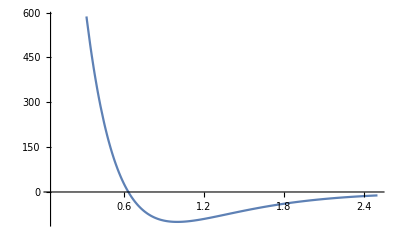

```mathematica
Plot[MorseLeft[1,100,rp,1.0],{rp,.05,2.5}]
```

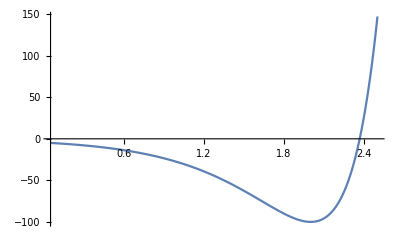

```mathematica
Plot[MorseRight[1,100,rp,1.0,3.0],{rp,.05,2.5}]
```

```mathematica
(*
Energies and wavefunctions for a Morse oscillator
from [J. P. Dahl, M. Springborg, J. Chem. Phys. 88, 4535 (1987)] 
(typo in Eq.(38): factor Sqrt[Alpha] is missing)
*)

(*
Energies of the discrete states
*)

(*
n = 0, 1, 2,... - quantum number;
Beta - Morse parameter (in 1/Bohr);
DE - dissociation energy (in kcal/mol);
M - mass of the particle (in Daltons);
MorseEnergy returns energy in kcal/mol relative to the bottom of the potential well.
*)

MorseEnergy[n_,Beta_,DE_,OptionsPattern[{M->MassH}]]:=Module[{DEA,Lambda,mu},
	DEA=DE*kcal2au;
	mu=OptionValue[M]*Dalton;
	Lambda=Sqrt[2*mu*DEA]/(hbar*Beta);
	au2kcal*hbar*((n+1/2)-1/(2*Lambda)*(n+1/2)^2)*Sqrt[(2*DEA*Beta^2)/mu]
];

(*
Number of bound states in Morse Potential:
Beta - beta parameter (1/Bohr);
DE - dissociation energy (kcal/mol);
M - mass (Daltons).
*)

MorseBound[Beta_,DE_,OptionsPattern[{M->MassH}]]:=Module[{DEA,Lambda,mu},
	DEA=DE*kcal2au;
	mu=OptionValue[M]*Dalton;
	Lambda=Sqrt[2*mu*DEA]/(hbar*Beta);
	IntegerPart[Lambda-1/2]
];
```

```mathematica
BetaMorse[ω1A,DE1A,mH]
```

0.00345833096 √(1/DE1A) ω1A

```mathematica
MorseEnergy[0,1.01,DE1A,Options[{M->MassH}]]
```

0.835011 (1/2-0.0521882/(√DE1A)) √DE1A

```mathematica
MorseEnergy[0,1.01,DE1A,Options[{M->MassD}]]
```

0.590588 (1/2-0.0369118/(√DE1A)) √DE1A

```mathematica
BetaMorse[ω2A,DE2A,mH]
```

0.00345833096 √(1/DE2A) ω2A

```mathematica
MorseEnergy[0,0.90,DE2A,Options[{M->MassH}]]
```

0.744069 (1/2-0.0465043/(√DE2A)) √DE2A

```mathematica
MorseEnergy[0,0.90,DE2A,Options[{M->MassD}]]
```

0.526267 (1/2-0.0328917/(√DE2A)) √DE2A

```mathematica
MorseEnergy[1,0.90,DE2A,Options[{M->MassD}]]
```

0.526267 (3/2-0.296025/(√DE2A)) √DE2A

```mathematica
5.544-2.652
```

2.892

```mathematica
2.892/0.8
```

3.615

## Calculation of ψ and concentration of HA as a function of distance from electrode, based on a Modified Gouy-Chapman-Stern Model of the Electrochemical Double Layer

```mathematica
ϕs::badη="The applied potential is anodic of (more positive than) -0.4 V vs. PZC: the ϕOHP expression used here is not valid. Returning Null.";
ϕs[T_,η_,x1A_,x2A_,εI_,ε_,c0ions_,xA_]:=Module[{p0,Langevin,u,n0ions,x1,x2,x,EII,εII,EI,ϕOHP,κ},
If[η>-0.40,Null;Message[ϕs::badη,η],
p0=(√(18 ε0 kB T (εw-n^2)/n0solv))/(2+n^2);
Langevin[u_]=Coth[u]-1/u;
n0ions=c0ions×NAvogadro×1000;
x1=x1A a2m;
x2=x2A a2m;
x=xA a2m;
ϕOHP=(2kB T)/elcharge ArcSinh[√(0.10/c0ions)Sinh[(elcharge (-0.130))/(2kB T)]];
εII[y_]:=n^2+(2+n^2)/(3 y ε0)n0solv p0  Langevin[(((2+n^2)p0 y)/(2 kB T))]; (* note that y here stands for EII below *)
EII=If[η==0,0,
NSolve[{y(x1 εII[y]/εI+x2)==η-ϕOHP},y,Reals]]⟦1,1,2⟧; (* in V/m *)
εII=n^2+(2+n^2)/(3 EII ε0)n0solv p0  Langevin[(((2+n^2)p0 EII)/(2 kB T))];
EI=EII*εII/εI;
κ=elcharge √((2n0ions)/(ε0 ε kB T));
Which[
xA<=x1A,η-x*EI,
x1A<xA<=x1A+x2A,η-x1*EI-(x-x1)EII,
xA>x1A+x2A,1/elcharge 4kB T ArcTanh[Tanh[(elcharge ϕOHP)/(4 kB T)]Exp[-κ(x-x1-x2)]]
]
]
];
```

```mathematica
WHAx::badE="The applied potential is anodic of (more positive than) -0.4 V vs. PZC: the ϕOHP expression used here is not valid. Returning Null.";
WHAx[T_,η_,x1A_,x2A_,εI_,ε_,c0ions_,WxminHA_,zHA_,xmin_,khar_,xA_]:=Module[{p0,Langevin,u,n0ions,x1,x2,x,EII,εII,EI,ϕOHP,κ,ϕx,WtotHA},
If[η>-0.40,Null;Message[ϕs::badη,η],
p0=(√(18 ε0 kB T (εw-n^2)/n0solv))/(2+n^2);
Langevin[u_]=Coth[u]-1/u;
n0ions=c0ions×NAvogadro×1000;
x1=x1A a2m;
x2=x2A a2m;
x=xA a2m;
ϕOHP=(2kB T)/elcharge ArcSinh[√(0.10/c0ions)Sinh[(elcharge (-0.130))/(2kB T)]];
εII[y_]:=n^2+(2+n^2)/(3 y ε0)n0solv p0  Langevin[(((2+n^2)p0 y)/(2 kB T))]; (* note that y here stands for EII below *)
EII=If[η==0,0,
NSolve[{y(x1 εII[y]/εI+x2)==η-ϕOHP},y,Reals]]⟦1,1,2⟧; (* in V/m *)
εII=n^2+(2+n^2)/(3 EII ε0)n0solv p0  Langevin[(((2+n^2)p0 EII)/(2 kB T))];
EI=EII*εII/εI;
κ=elcharge √((2n0ions)/(ε0 ε kB T));
ϕx=Which[
xA<=x1A,η-x*EI,
x1A<xA<=x1A+x2A,η-x1*EI-(x-x1)EII,
xA>x1A+x2A,1/elcharge 4kB T ArcTanh[Tanh[(elcharge ϕOHP)/(4 kB T)]Exp[-κ(x-x1-x2)]]
];
zHA*ϕx+WxminHA+(khar*(x-xmin*a2m)^2*J2ev)/2 
(* total work term, electrostatic and non-electrostatic, for HA at x, in eV *)

]
];
```

```mathematica
cHAx::badη="The applied potential is anodic of (more positive than) -0.4 V vs. PZC: the ϕOHP expression used here is not valid. Returning Null.";
cHAx[T_,η_,x1A_,x2A_,εI_,ε_,c0ions_,WxminHA_,zHA_,xmin_,khar_,cHA_,xA_]:=Module[{p0,Langevin,u,n0ions,x1,x2,x,EII,εII,EI,ϕOHP,κ,ϕx,WtotHA},
If[η>-0.40,Null;Message[ϕs::badη,η],
p0=(√(18 ε0 kB T (εw-n^2)/n0solv))/(2+n^2);
Langevin[u_]=Coth[u]-1/u;
n0ions=c0ions×NAvogadro×1000;
x1=x1A a2m;
x2=x2A a2m;
x=xA a2m;
ϕOHP=(2kB T)/elcharge ArcSinh[√(0.10/c0ions)Sinh[(elcharge (-0.130))/(2kB T)]];
εII[y_]:=n^2+(2+n^2)/(3 y ε0)n0solv p0  Langevin[(((2+n^2)p0 y)/(2 kB T))]; (* note that y here stands for EII below *)
EII=If[η==0,0,
NSolve[{y(x1 εII[y]/εI+x2)==η-ϕOHP},y,Reals]]⟦1,1,2⟧; (* in V/m *)
εII=n^2+(2+n^2)/(3 EII ε0)n0solv p0  Langevin[(((2+n^2)p0 EII)/(2 kB T))];
EI=EII*εII/εI;
κ=elcharge √((2n0ions)/(ε0 ε kB T));
ϕx=Which[
xA<=x1A,η-x*EI,
x1A<xA<=x1A+x2A,η-x1*EI-(x-x1)EII,
xA>x1A+x2A,1/elcharge 4kB T ArcTanh[Tanh[(elcharge ϕOHP)/(4 kB T)]Exp[-κ(x-x1-x2)]]
];
WtotHA=zHA*ϕx+WxminHA+(khar*(x-xmin*a2m)^2*J2ev)/2; (* total work term, electrostatic and non-electrostatic, for HA at x, in eV *)
cHA*Exp[-WtotHA*ev2au/kb/T]
]
];
```

## Solution Phase FES Incorporating Effects of Applied Potential and EDL

Construction of Solution Phase FES at each R, as functions of Proton Coordinate rp and Collective Solvent Coordinate X  
Input parameters:
DE1 - dissociation energy (kcal/mol);

	DE2 - dissociation energy (kcal/mol);
	ω1 - vibrational frequency (cm-1);
	ω2- beta parameter (cm-1);
	W - coupling between reactant and product diabatic states at donor-acceptor distance of 3.0 Å,in kcal/mol; 
	ΔGatSHE - ΔG for Volmer reaction at SHE,in kcal/mol;
	SHE - SHE vs. E_PZC,in V;
	X - diabatic solvation energy gap,in kcal/mol; 
	λ - solvent reorganization energy,in kcal/mol; 
	γ - half band width in semi-elliptical DOS,in kcal/mol; 
	T - temperature,in K; 
	x1A - distance of contact layer plane (CLP) from electrode surface,in Å;
	x2A - distance of outer Helmholtz plane (OHP) from CLP,in Å
	εI - relative permittivity (dielectric constant) of contact layer (CL), assumed independent of η;
	ε - relative permittivity of diffuse layer,assumed independent of E and equal to pure bulk solvent; 
	c0ions - concentration of cations in solution containing only monovalent ions,in M;
	xA - distance from electrode surface,in Å,usually set equal to R;
        WxminHA -- work term for moving HA from bulk solution to xmin (vide infra), in eV;
        WxminA -- work term for moving A from bulk solution to xmin (vide infra), in eV;
        zHA -- charge of HA;
	R - distance between donor and acceptor,in Å; 
	E- applied potential,in V vs. E_PZC; 
	rp- proton coordinate / O-H distance,in Å; 

Select local variables:      
 G1 - solution phase free energy of reactant state, in kcal/mol;
	ΔGelst -  reaction free energy contribution of electric field, in kcal/mol;
	ΔGkF - Volmer reaction free energy for reaction involving an electron at Fermi level, in kcal/mol;
	Vk - electronic coupling between reactant and product diabatic states at donor-acceptor distance,assumed to decay exponentially with distance (β = 1.0 Å^-1).

Ground-state solution-phase FES at fixed R and E: Semi-elliptical distribution used to model DOS of d- and sp-bands; zero set at Fermi level;EDL effects incorporated into reactant and product diabatic FESes

```mathematica
DE1A=7.37ev2kcal;ω1A=3536;DE2A=52.14;ω2A=1880;rDH=0.976;rAH=1.60;ΔGatSHEA=0.41ev2kcal+10;SHEA=-(0.244+0.24);λA=10.0;
γA=70;TT=298;xCL=3.2;xOHL=3.5;εCLA=4.2;
c0ionsA=0.10;
```

```mathematica
zH3O=1;
WxminHA=0.3;
kharA=25;
```

Ground-state solution-phase FES at fixed R and E: Semi-elliptical distribution used to model DOS of d- and sp-bands; zero set at Fermi level;EDL effects incorporated into reactant and product diabatic FESes

```mathematica
DE1A=7.37ev2kcal;ω1A=3536;DE2A=52.14;ω2A=1880;rDH=0.976;rAH=1.60;ΔGatSHEA=0.41ev2kcal+10;SHEA=-(0.244+0.24);λA=10.0;
γA=70;TT=298;xCL=3.2;xOHL=3.5;εCLA=4.2;
c0ionsA=0.10;
```

```mathematica
zH3O=1;
WxminHA=0.3;
kharA=25;
```

#### Quantization of Solution Phase FES along Proton Coordinate by solving 1D Schrodinger Equation at each X (and R)

Input parameters:
DE1 - dissociation energy (kcal/mol);
	DE2 - dissociation energy (kcal/mol);
	ω1 - vibrational frequency (cm-1);
	ω2- beta parameter (cm-1);
	W - coupling between reactant and product diabatic states at donor-acceptor distance of 3.0 Å,in kcal/mol; 
	ΔGatSHE - ΔG for Volmer reaction at SHE,in kcal/mol;
	SHE - SHE vs. E_PZC,in V;
	X - diabatic solvation energy gap,in kcal/mol; 
	λ - solvent reorganization energy,in kcal/mol; 
	γ - half band width in semi-elliptical DOS,in kcal/mol; 
	T - temperature,in K; 
	x1A - distance of contact layer plane (CLP) from electrode surface,in Å;
	x2A - distance of outer Helmholtz plane (OHP) from CLP,in Å
	εI - relative permittivity (dielectric constant) of contact layer (CL), assumed independent of η;
	ε - relative permittivity of diffuse layer,assumed independent of E and equal to pure bulk solvent; 
	c0ions - concentration of cations in solution containing only monovalent ions,in M;
	xA - distance from electrode surface,in Å,usually set equal to R;
        WxminHA - work term for moving HA from bulk solution to xmin (vide infra), in eV;
        WxminA - work term for moving A from bulk solution to xmin (vide infra), in eV;
        zHA - charge of HA;
	R - distance between donor and acceptor,in Å; 
	E- applied potential,in V vs. E_PZC; 
	δ - grid size,in Å;
	nRoots - number of roots to Schrodinger equation to be obtained;

Select local variables:      
 μ - reduced mass,in amu;
	KE - kinetic energy,in au.

Ground-state solution-phase FES at fixed R and E: Semi-elliptical distribution used to model DOS of d-band;  zero set at top of band;EDL effects incorporated into reactant and product diabatic FESes

```mathematica
DiagGSFixedRQuiet[Vd_,Vsp_,ΔGatSHE_,SHE_,X_,λ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,WxminHA_,zHA_,khar_,R_,E_,ϵc_,γd_,γsp_,δ_,nRoots_,OptionsPattern[{M->mH,DiffOrder->4}]]:=
Module[{Ggrid,Gmin,Fgrid,nOrder,dims,ndim,Ranges,tuples,μ,KE,DiagMat,h,en,v,WvFn1,WvFn2,EigenVals},
Ggrid=ParallelTable[SolGSFixedRQuiet[Vd,Vsp,ΔGatSHE,SHE,X,λ,T,x1A,x2A,εI,ε,c0ions,WxminHA,zHA,khar,R,E,ϵc,γd,γsp,rp]*kcal2au,{rp,0.7,R-rAH+0.35,δ}];
Gmin=Min[Ggrid];
Fgrid=Ggrid-Gmin;
nOrder=OptionValue[DiffOrder];
dims=Dimensions[Fgrid];
ndim=Length[dims];
Ranges=Table[Range[1,dims⟦idim⟧],{idim,1,ndim}];
tuples=Tuples[Ranges];
μ=OptionValue[M];
KE=-1/(2 μ (δ*a2bohr)^2) Sum[
NDSolve`FiniteDifferenceDerivative[i,Ranges,"DifferenceOrder"->nOrder]["DifferentiationMatrix"],
{i,DiagonalMatrix[Table[2,{i,1,ndim}]]}];
DiagMat=DiagonalMatrix[SparseArray[(Fgrid⟦##⟧&@@@tuples)]];
h=N[KE+DiagMat];
en=Reverse@Re@Eigenvalues[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
v=Reverse@Re@Eigenvectors[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
EigenVals=({en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}⟦1⟧+Gmin)au2kcal;
Min[EigenVals]
];
```

```mathematica
DiagFixedRQuiet[Vd_,Vsp_,ΔGatSHE_,SHE_,X_,λ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,WxminHA_,zHA_,khar_,R_,E_,ϵc_,γd_,γsp_,δ_,nRoots_,OptionsPattern[{M->mH,DiffOrder->4}]]:=
Module[{Ggrid,Gmin,Fgrid,nOrder,dims,ndim,Ranges,tuples,μ,KE,DiagMat,h,en,v,WvFn1,WvFn2,EigenVals},
Ggrid=ParallelTable[SolGSFixedRQuiet[Vd,Vsp,ΔGatSHE,SHE,X,λ,T,x1A,x2A,εI,ε,c0ions,WxminHA,zHA,khar,R,E,ϵc,γd,γsp,rp]*kcal2au,{rp,0.7,R-rAH+0.35,δ}];
Gmin=Min[Ggrid];
Fgrid=Ggrid-Gmin;
nOrder=OptionValue[DiffOrder];
dims=Dimensions[Fgrid];
ndim=Length[dims];
Ranges=Table[Range[1,dims⟦idim⟧],{idim,1,ndim}];
tuples=Tuples[Ranges];
μ=OptionValue[M];
KE=-1/(2 μ (δ*a2bohr)^2) Sum[
NDSolve`FiniteDifferenceDerivative[i,Ranges,"DifferenceOrder"->nOrder]["DifferentiationMatrix"],
{i,DiagonalMatrix[Table[2,{i,1,ndim}]]}];
DiagMat=DiagonalMatrix[SparseArray[(Fgrid⟦##⟧&@@@tuples)]];
h=N[KE+DiagMat];
en=Reverse@Re@Eigenvalues[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
v=Reverse@Re@Eigenvectors[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
EigenVals=({en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}⟦1⟧+Gmin)au2kcal;
{Min[EigenVals],RankedMin[EigenVals,2],RankedMin[EigenVals,3],RankedMin[EigenVals,4]}
];
```

```mathematica
Diag1DFES[Vd_,Vsp_,ΔGatSHE_,SHE_,λ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,WxminHA_,zHA_,khar_,R_,E_,ϵc_,γd_,γsp_,δ_,nRoots_,OptionsPattern[{M->mH,DiffOrder->4}]]:=Module[{nOrder,μ,,tab1,tabGS,tabEx1,tabEx2,tabEx3},
μ=OptionValue[M];
nOrder=OptionValue[DiffOrder];
tab1=Table[DiagFixedRQuiet[Vd,Vsp,ΔGatSHE,SHE,X,λ,T,x1A,x2A,εI,ε,c0ions,WxminHA,zHA,khar,R,E,ϵc,γd,γsp,δ,nRoots,M->μ,DiffOrder->nOrder],{X,-2.5λ,2.5λ,λ/10}];
tabGS=Table[{(-2.5+n/10)λ,tab1⟦n+1,1⟧},{n,0,50,1}];Print[tabGS];
tabEx1=Table[{(-2.5+n/10)λ,tab1⟦n+1,2⟧},{n,0,50,1}];Print[tabEx1];
tabEx2=Table[{(-2.5+n/10)λ,tab1⟦n+1,3⟧},{n,0,50,1}];Print[tabEx2];
tabEx3=Table[{(-2.5+n/10)λ,tab1⟦n+1,4⟧},{n,0,50,1}];Print[tabEx3];
ListLinePlot[
{tabGS,tabEx1,tabEx2,tabEx3},
PlotLegends->{"Vibrational Ground State","1st Excited State","2nd Excited State","3rd Excited State"},ImageSize->Large,
Frame->True,FrameLabel->{"X, kcal mol^-1","G, kcal mol^-1"},FrameStyle->Directive[FontFamily->"Helvetica",15,Black],Axes->False,
LabelStyle->{FontFamily->"Helvetica",12,GrayLevel[0]},PlotLabel->StringForm["R = `` Å; V_d = `` kcal mol^-1; V_sp = `` kcal mol^-1; E = `` V; k_har = `` J m^-2",R,Vd,Vsp,E,khar]
]
]
```

#### Construction of proton - quantized 2 D - FES as function of X and R

Input parameters:
    DE1 - dissociation energy (kcal/mol);
	DE2 - dissociation energy (kcal/mol);
	ω1 - vibrational frequency (cm-1);
	ω2- beta parameter (cm-1);
	W - coupling between reactant and product diabatic states at donor-acceptor distance of 3.0 Å,in kcal/mol; 
	ΔGatSHE - ΔG for Volmer reaction at SHE,in kcal/mol;
	SHE - SHE vs. E_PZC,in V;
	X - diabatic solvation energy gap,in kcal/mol; 
	λ - solvent reorganization energy,in kcal/mol; 
	γ - half band width in semi-elliptical DOS,in kcal/mol; 
	T - temperature,in K; 
	x1A - distance of contact layer plane (CLP) from electrode surface,in Å;
	x2A - distance of outer Helmholtz plane (OHP) from CLP,in Å
	εI - relative permittivity (dielectric constant) of contact layer (CL), assumed independent of η;
	ε - relative permittivity of diffuse layer,assumed independent of E and equal to pure bulk solvent; 
	c0ions - concentration of cations in solution containing only monovalent ions,in M;
	xA - distance from electrode surface,in Å,usually set equal to R;
        WxminHA - work term for moving HA from bulk solution to xmin (vide infra), in eV;
        WxminA - work term for moving A from bulk solution to xmin (vide infra), in eV;
        zHA - charge of HA;
	R - distance between donor and acceptor,in Å; 
	E- applied potential,in V vs. E_PZC; 
	δ - grid size for proton coordinate,in Å;
	nRoots - number of roots to Schrodinger equation to be obtained;
	Xmin - minimum X (for plotting purposes), in kcal/mol;
	Xmin - minimum X (for plotting purposes), in kcal/mol;
     δR - grid size for R,in Å;

Ground-state solution-phase FES at fixed R and E: Semi-elliptical distribution used to model DOS of d- and sp-bands;  zero set at Fermi level;EDL effects incorporated into reactant and product diabatic FESes

```mathematica
TSandRXR[Vd_,Vsp_,ΔGatSHE_,SHE_,λ_,T_,x1A_,x2A_,εI_,ε_,c0ions_,WxminHA_,zHA_,khar_,E_,ϵc_,γd_,γsp_,δ_,nRoots_,OptionsPattern[{M->mH,DiffOrder->4}]]:=
Module[
{nOrder,μ,Xmin,Xmax,tabR,tabP,minR,table,max1,max2,max3,max4,max5,max6,max7,max8,max9,TS,NContours},
μ=OptionValue[M];
nOrder=OptionValue[DiffOrder];
Xmin=-1.1λ;
Xmax=1.1λ;
tabR=Table[{X,R,DiagGSFixedRQuiet[Vd,Vsp,ΔGatSHE,SHE,X,λ,T,x1A,x2A,εI,ε,c0ions,WxminHA,zHA,khar,R,E,ϵc,γd,γsp,δ,nRoots,M->μ,DiffOrder->nOrder]},{R,2.95,3.25,0.05},{X,0,Xmax,λ/20}];
tabP=Table[{X,R,DiagGSFixedRQuiet[Vd,Vsp,ΔGatSHE,SHE,X,λ,T,x1A,x2A,εI,ε,c0ions,WxminHA,zHA,khar,R,E,ϵc,γd,γsp,δ,nRoots,M->μ,DiffOrder->nOrder]},{R,2.95,3.25,0.05},{X,Xmin,0,λ/20}];
minR=MinimalBy[Flatten[tabR,1],Last] ;Print["Reactant well: ",minR⟦1,3⟧," kcal/mol"];
max1=MaximalBy[tabP⟦1⟧,Last];Print["TS at 2.95 Å",max1];
max2=MaximalBy[tabP⟦2⟧,Last];Print["TS at 3.00 Å",max2];
max3=MaximalBy[tabP⟦3⟧,Last];Print["TS at 3.05 Å",max3];
max4=MaximalBy[tabP⟦4⟧,Last];Print["TS at 3.10 Å",max4];
max5=MaximalBy[tabP⟦5⟧,Last];Print["TS at 3.15 Å",max5];
max6=MaximalBy[tabP⟦6⟧,Last];Print["TS at 3.20 Å",max6];
max7=MaximalBy[tabP⟦7⟧,Last];Print["TS at 3.25 Å",max7];
TS=MinimalBy[Join[max1,max2,max3,max4,max5,max6,max7],Last]⟦1⟧;
Print["Saddle point: ",TS⟦3⟧," kcal/mol"];
table=Join[tabR,tabP];
NContours=80;
Print[
ListContourPlot[
Flatten[table,1],PlotLegends->Automatic,ImageSize->Large,Frame->True,FrameLabel->{"X, kcal mol^-1","R, Å"},FrameStyle->Directive[FontFamily->"Helvetica",15,Black],Axes->False,PlotLabel->StringForm["V_d = `` kcal mol^-1; V_sp = `` kcal mol^-1; E = `` V; λ = `` kcal mol^-1; k_har = `` J m^-2",Vd,Vsp,E,λ,khar],LabelStyle->{FontFamily->"Helvetica",12,GrayLevel[0]},Contours->NContours,ColorFunction->"Rainbow"
]
];
{minR,TS}
]
```

```mathematica
(* Proton-quantized 2D PES, H *)
```

Reactant well: 8.86294 kcal/mol

TS at 2.95 Å{{-16.5,2.95,19.1426}}

TS at 3.00 Å{{-16.5,3.,16.5125}}

TS at 3.05 Å{{-9.75,3.05,14.2736}}

TS at 3.10 Å{{-6.75,3.1,13.2346}}

TS at 3.15 Å{{-4.5,3.15,12.9691}}

TS at 3.20 Å{{-2.25,3.2,13.4952}}

TS at 3.25 Å{{-0.75,3.25,14.5569}}

Saddle point: 12.9691 kcal/mol

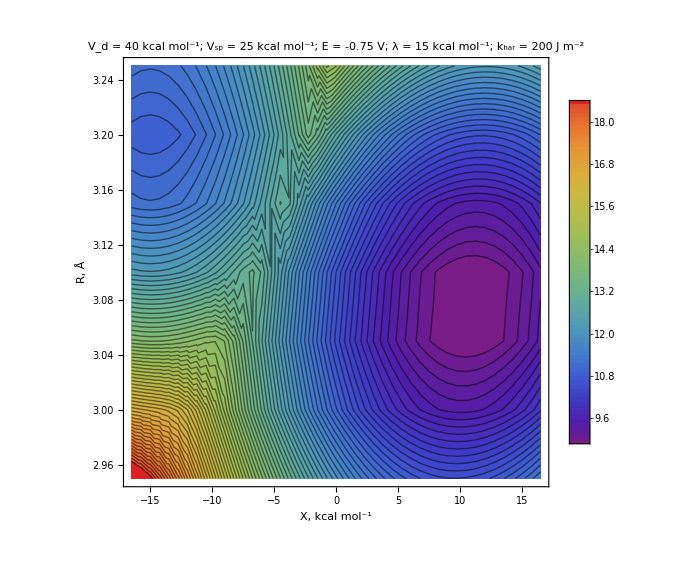

{{{45/4,3.1,8.86294}},{-4.5,3.15,12.9691}}

```mathematica
TSandRXR[40,25,0.62ev2kcal,SHEA,15,TT,xCL,xOHL,εCLA,εw,c0ionsA,0.9,zH3O,200,-0.75,-90,60,200,0.005,60,Options[{M->mH,DiffOrder->2}]]
```

```mathematica
(* Vibrational ground state and first three excited states at reactant well R *)
```

{{-37.5,21.503},{-36.,20.4155},{-34.5,19.403},{-33.,18.4654},{-31.5,17.6029},{-30.,16.8153},{-28.5,16.1027},{-27.,15.4651},{-25.5,14.9024},{-24.,14.4146},{-22.5,14.0016},{-21.,13.6634},{-19.5,13.3999},{-18.,13.2109},{-16.5,13.0962},{-15.,13.0555},{-13.5,13.088},{-12.,13.1922},{-10.5,13.3636},{-9.,13.5783},{-7.5,13.5279},{-6.,12.894},{-4.5,12.2259},{-3.,11.6023},{-1.5,11.0346},{0.,10.527},{1.5,10.0821},{3.,9.70142},{4.5,9.38606},{6.,9.13695},{7.5,8.95481},{9.,8.84024},{10.5,8.79372},{12.,8.81569},{13.5,8.90649},{15.,9.06644},{16.5,9.29581},{18.,9.5949},{19.5,9.96407},{21.,10.4036},{22.5,10.9137},{24.,11.4944},{25.5,12.146},{27.,12.8686},{28.5,13.6623},{30.,14.5273},{31.5,15.4637},{33.,16.4717},{34.5,17.5513},{36.,18.7028},{37.5,19.9262}}

{{-37.5,26.6007},{-36.,25.5129},{-34.5,24.4999},{-33.,23.5615},{-31.5,22.6976},{-30.,21.9077},{-28.5,21.1915},{-27.,20.5484},{-25.5,19.9775},{-24.,19.4774},{-22.5,19.0459},{-21.,18.679},{-19.5,18.3694},{-18.,18.1008},{-16.5,17.833},{-15.,17.4688},{-13.5,16.8878},{-12.,16.1315},{-10.5,15.3225},{-9.,14.5479},{-7.5,14.143},{-6.,14.4383},{-4.5,14.8897},{-3.,15.4196},{-1.5,16.0115},{0.,16.641},{1.5,17.2291},{3.,17.5523},{4.5,17.5639},{6.,17.4869},{7.5,17.4195},{9.,17.3915},{10.5,17.4147},{12.,17.495},{13.5,17.6358},{15.,17.8388},{16.5,18.1051},{18.,18.4365},{19.5,18.8368},{21.,19.3075},{22.5,19.8473},{24.,20.4557},{25.5,21.133},{27.,21.8797},{28.5,22.6961},{30.,23.5826},{31.5,24.5395},{33.,25.567},{34.5,26.6653},{36.,27.8345},{37.5,29.0749}}

{{-37.5,31.413},{-36.,30.3215},{-34.5,29.3014},{-33.,28.3507},{-31.5,27.4663},{-30.,26.6444},{-28.5,25.8786},{-27.,25.1597},{-25.5,24.4725},{-24.,23.7941},{-22.5,23.0921},{-21.,22.3334},{-19.5,21.5059},{-18.,20.6365},{-16.5,19.7947},{-15.,19.1066},{-13.5,18.7129},{-12.,18.5845},{-10.5,18.6059},{-9.,18.707},{-7.5,18.8426},{-6.,18.9649},{-4.5,19.019},{-3.,18.9683},{-1.5,18.8301},{0.,18.6698},{1.5,18.6072},{3.,18.8923},{4.5,19.5864},{6.,20.4718},{7.5,21.4466},{9.,22.4634},{10.5,23.4648},{12.,24.3552},{13.5,25.0489},{15.,25.5794},{16.5,26.0257},{18.,26.4438},{19.5,26.9458},{21.,27.5344},{22.5,28.1651},{24.,28.8426},{25.5,29.5756},{27.,30.3694},{28.5,31.2268},{30.,32.1499},{31.5,33.1399},{33.,34.1977},{34.5,35.324},{36.,36.5195},{37.5,37.7844}}

{{-37.5,35.9121},{-36.,34.7991},{-34.5,33.7396},{-33.,32.7228},{-31.5,31.7365},{-30.,30.7669},{-28.5,29.8008},{-27.,28.8301},{-25.5,27.8596},{-24.,26.9123},{-22.5,26.0298},{-21.,25.26},{-19.5,24.6325},{-18.,24.1422},{-16.5,23.7596},{-15.,23.4493},{-13.5,23.1771},{-12.,22.9135},{-10.5,22.6385},{-9.,22.3507},{-7.5,22.0749},{-6.,21.8628},{-4.5,21.7822},{-3.,21.8831},{-1.5,22.1606},{0.,22.5685},{1.5,23.0537},{3.,23.5683},{4.5,24.0701},{6.,24.5299},{7.5,24.9459},{9.,25.3516},{10.5,25.8189},{12.,26.4612},{13.5,27.3744},{15.,28.5201},{16.5,29.7622},{18.,30.4907},{19.5,31.7717},{21.,33.5423},{22.5,34.8371},{24.,35.9452},{25.5,36.9685},{27.,37.9647},{28.5,38.9696},{30.,40.0046},{31.5,41.0828},{33.,42.2123},{34.5,43.3986},{36.,44.6453},{37.5,45.955}}

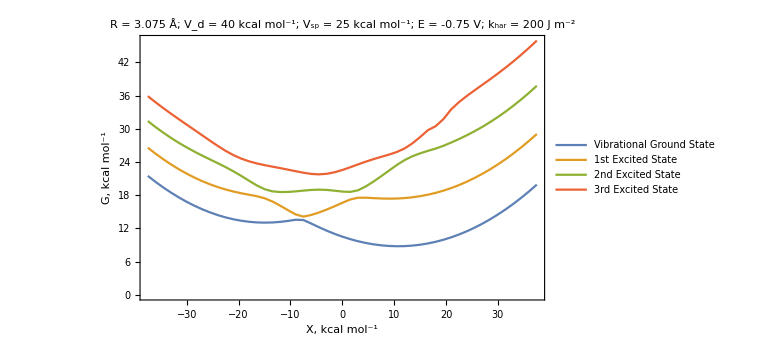

```mathematica
Diag1DFES[40,25,0.62ev2kcal,SHEA,15,TT,xCL,xOHL,εCLA,εw,c0ionsA,0.9,zH3O,200,3.075,-0.75,-90,60,200,0.005,4,Options[{M->mH,DiffOrder->2}]]
```

```mathematica
(* Vibrational ground state and first three excited states at saddle point R *)
```

{{-37.5,19.6139},{-36.,18.5264},{-34.5,17.5139},{-33.,16.5764},{-31.5,15.7139},{-30.,14.9264},{-28.5,14.2138},{-27.,13.5763},{-25.5,13.0138},{-24.,12.5263},{-22.5,12.1138},{-21.,11.7762},{-19.5,11.5136},{-18.,11.326},{-16.5,11.2134},{-15.,11.1757},{-13.5,11.2128},{-12.,11.3249},{-10.5,11.5116},{-9.,11.773},{-7.5,12.1086},{-6.,12.5168},{-4.5,12.9691},{-3.,12.5442},{-1.5,11.9427},{0.,11.3998},{1.5,10.9201},{3.,10.5056},{4.5,10.1574},{6.,9.87628},{7.5,9.66304},{9.,9.51819},{10.5,9.44218},{12.,9.43541},{13.5,9.49821},{15.,9.63087},{16.5,9.83361},{18.,10.1066},{19.5,10.4502},{21.,10.8647},{22.5,11.3504},{24.,11.9074},{25.5,12.5357},{27.,13.2355},{28.5,14.007},{30.,14.8502},{31.5,15.7653},{33.,16.7524},{34.5,17.8116},{36.,18.9431},{37.5,20.1469}}

{{-37.5,24.7117},{-36.,23.6242},{-34.5,22.6117},{-33.,21.6741},{-31.5,20.8115},{-30.,20.0238},{-28.5,19.311},{-27.,18.6729},{-25.5,18.1096},{-24.,17.6209},{-22.5,17.2066},{-21.,16.8663},{-19.5,16.5997},{-18.,16.4061},{-16.5,16.2839},{-15.,16.2303},{-13.5,16.2375},{-12.,16.2735},{-10.5,16.1362},{-9.,15.4964},{-7.5,14.7136},{-6.,13.9496},{-4.5,13.2617},{-3.,13.5806},{-1.5,14.2094},{0.,14.9156},{1.5,15.6945},{3.,16.542},{4.5,17.4412},{6.,18.1992},{7.5,18.2722},{9.,18.2269},{10.5,18.2195},{12.,18.2675},{13.5,18.3763},{15.,18.5486},{16.5,18.7854},{18.,19.0869},{19.5,19.4543},{21.,19.8937},{22.5,20.406},{24.,20.9879},{25.5,21.6392},{27.,22.3602},{28.5,23.1516},{30.,24.0135},{31.5,24.9464},{33.,25.9504},{34.5,27.0257},{36.,28.1726},{37.5,29.391}}

{{-37.5,29.527},{-36.,28.4391},{-34.5,27.4258},{-33.,26.4867},{-31.5,25.6213},{-30.,24.829},{-28.5,24.1088},{-27.,23.4593},{-25.5,22.8782},{-24.,22.3618},{-22.5,21.9035},{-21.,21.4903},{-19.5,21.0946},{-18.,20.6558},{-16.5,20.0748},{-15.,19.3093},{-13.5,18.4401},{-12.,17.5799},{-10.5,16.9749},{-9.,16.9746},{-7.5,17.2292},{-6.,17.5798},{-4.5,17.991},{-3.,18.4298},{-1.5,18.8257},{0.,19.0395},{1.5,19.0083},{3.,18.8551},{4.5,18.6999},{6.,18.7803},{7.5,19.6591},{9.,20.7778},{10.5,21.9827},{12.,23.2523},{13.5,24.5603},{15.,25.8112},{16.5,26.7088},{18.,27.2342},{19.5,27.6127},{21.,28.1727},{22.5,28.8289},{24.,29.4974},{25.5,30.2084},{27.,30.9761},{28.5,31.8065},{30.,32.7024},{31.5,33.6655},{33.,34.6969},{34.5,35.7974},{36.,36.9675},{37.5,38.2077}}

{{-37.5,34.0419},{-36.,32.9501},{-34.5,31.9285},{-33.,30.9732},{-31.5,30.0796},{-30.,29.2411},{-28.5,28.4474},{-27.,27.6834},{-25.5,26.9259},{-24.,26.1444},{-22.5,25.3106},{-21.,24.42},{-19.5,23.5108},{-18.,22.6711},{-16.5,22.0277},{-15.,21.6446},{-13.5,21.4581},{-12.,21.3866},{-10.5,21.3755},{-9.,21.3793},{-7.5,21.3497},{-6.,21.2448},{-4.5,21.0592},{-3.,20.8429},{-1.5,20.7033},{0.,20.8105},{1.5,21.2471},{3.,21.9013},{4.5,22.6664},{6.,23.4804},{7.5,24.2862},{9.,25.0138},{10.5,25.608},{12.,26.0852},{13.5,26.5253},{15.,27.0726},{16.5,28.0458},{18.,29.4401},{19.5,30.3931},{21.,32.1723},{22.5,34.2937},{24.,35.9288},{25.5,37.3374},{27.,38.5146},{28.5,39.5819},{30.,40.63},{31.5,41.7007},{33.,42.8135},{34.5,43.9785},{36.,45.2017},{37.5,46.4869}}

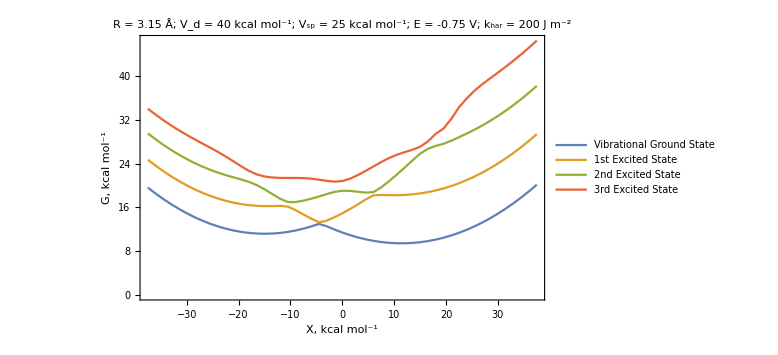

```mathematica
Diag1DFES[40,25,0.62ev2kcal,SHEA,15,TT,xCL,xOHL,εCLA,εw,c0ionsA,0.9,zH3O,200,3.15,-0.75,-90,60,200,0.005,4,Options[{M->mH,DiffOrder->2}]]
```

```mathematica
(* Proton potential at saddle point X and R *)
```

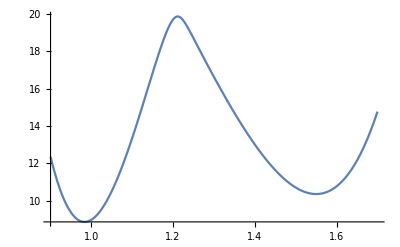

```mathematica
Plot[SolGSFixedRQuiet[40,25,0.62ev2kcal,SHEA,-4.5,15,TT,xCL,xOHL,εCLA,εw,c0ionsA,0.9,zH3O,200,3.15,-0.75,-90,60,200,rp],{rp,0.9,1.7},PlotPoints->100]
```

```mathematica
(* Proton potential at saddle point X *)
```

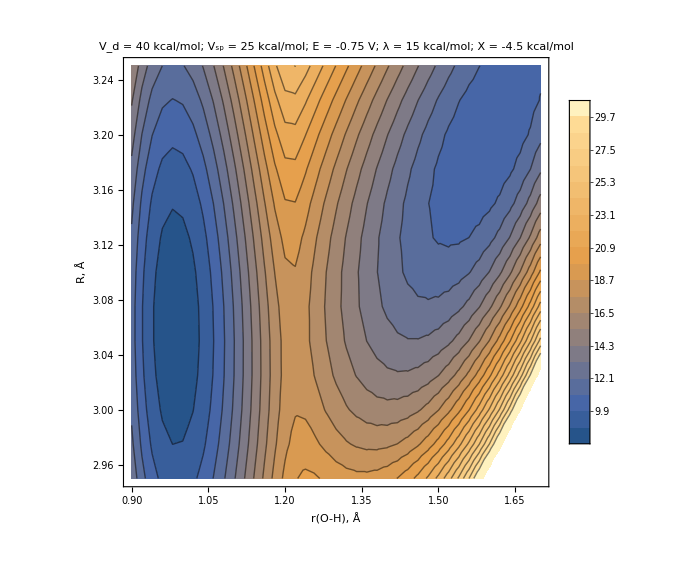

```mathematica
ListContourPlot[Flatten[Table[{rp,R,SolGSFixedRQuiet[40,25,0.62ev2kcal,SHEA,-4.5,15,TT,xCL,xOHL,εCLA,εw,c0ionsA,0.9,zH3O,200,R,-0.75,-90,60,200,rp]},{rp,0.90,1.70,0.02},{R,2.95,3.25,0.025}],1],PlotLegends->Automatic,Contours->20,ImageSize->Large,Frame->True,FrameLabel->{"r(O-H), Å","R, Å"},FrameStyle->Directive[FontFamily->"Helvetica",12,Black],Axes->False,PlotLabel->StringForm["V_d = 40 kcal/mol; V_sp = 25 kcal/mol; E = -0.75 V; λ = 15 kcal/mol; X = -4.5 kcal/mol"],LabelStyle->{FontFamily->"Helvetica",12,GrayLevel[0]}
]
```

```mathematica
(* Proton-quantized 2D PES, H *)
```

Reactant well: 8.60153 kcal/mol

TS at 2.95 Å{{-11.,2.95,16.6924}}

TS at 3.00 Å{{-11.,3.,13.7941}}

TS at 3.05 Å{{-11.,3.05,12.178}}

TS at 3.10 Å{{-11.,3.1,11.7235}}

TS at 3.15 Å{{-11.,3.15,11.1215}}

TS at 3.20 Å{{-1.5,3.2,12.0141}}

TS at 3.25 Å{{0.,3.25,13.9459}}

Saddle point: 11.1215 kcal/mol

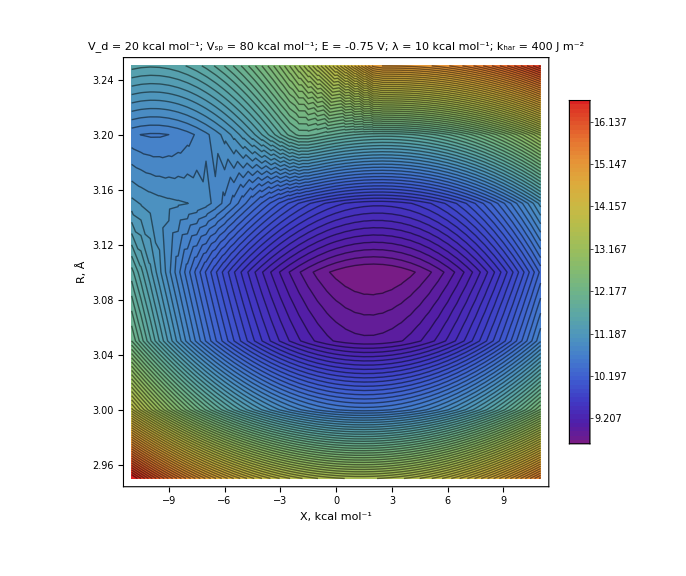

{{{2,3.1,8.60153}},{-11.,3.15,11.1215}}

```mathematica
TSandRXR[20,80,0.62ev2kcal,SHEA,10,TT,xCL,xOHL,εCLA,εw,c0ionsA,1.7,zH3O,400,-0.75,-90,60,200,0.005,30,Options[{M->mH,DiffOrder->2}]]
```

```mathematica
(* Vibrational ground state and first three excited states at reactant well R *)
```

{{-25.,18.8471},{-24.,18.0883},{-23.,17.3763},{-22.,16.7107},{-21.,16.0908},{-20.,15.5159},{-19.,14.9846},{-18.,14.4953},{-17.,14.0453},{-16.,13.6302},{-15.,13.2431},{-14.,12.8729},{-13.,12.5042},{-12.,12.1222},{-11.,11.7235},{-10.,11.3176},{-9.,10.9188},{-8.,10.5384},{-7.,10.184},{-6.,9.86019},{-5.,9.57008},{-4.,9.31574},{-3.,9.0986},{-2.,8.91974},{-1.,8.77999},{0.,8.68002},{1.,8.62038},{2.,8.60153},{3.,8.6239},{4.,8.68783},{5.,8.79365},{6.,8.94165},{7.,9.13212},{8.,9.36528},{9.,9.64139},{10.,9.96065},{11.,10.3233},{12.,10.7295},{13.,11.1794},{14.,11.6732},{15.,12.2112},{16.,12.7933},{17.,13.4199},{18.,14.091},{19.,14.8069},{20.,15.5675},{21.,16.3731},{22.,17.2238},{23.,18.1197},{24.,19.0609},{25.,20.0476}}

{{-25.,22.4568},{-24.,21.5463},{-23.,20.6655},{-22.,19.8136},{-21.,18.9901},{-20.,18.1954},{-19.,17.4307},{-18.,16.6982},{-17.,16.0012},{-16.,15.3448},{-15.,14.7368},{-14.,14.1889},{-13.,13.7173},{-12.,13.3371},{-11.,13.0519},{-10.,12.8519},{-9.,12.7226},{-8.,12.6519},{-7.,12.6311},{-6.,12.6538},{-5.,12.7149},{-4.,12.8095},{-3.,12.9332},{-2.,13.0815},{-1.,13.2504},{0.,13.437},{1.,13.6397},{2.,13.8586},{3.,14.0951},{4.,14.3517},{5.,14.6313},{6.,14.9368},{7.,15.2706},{8.,15.6352},{9.,16.0324},{10.,16.4639},{11.,16.9311},{12.,17.4351},{13.,17.9769},{14.,18.5573},{15.,19.177},{16.,19.8366},{17.,20.5368},{18.,21.278},{19.,22.0606},{20.,22.8851},{21.,23.7517},{22.,24.6609},{23.,25.6128},{24.,26.6079},{25.,27.6463}}

{{-25.,25.0195},{-24.,24.081},{-23.,23.1935},{-22.,22.358},{-21.,21.575},{-20.,20.8444},{-19.,20.1655},{-18.,19.5373},{-17.,18.9584},{-16.,18.4272},{-15.,17.9419},{-14.,17.501},{-13.,17.103},{-12.,16.7465},{-11.,16.4306},{-10.,16.1545},{-9.,15.9181},{-8.,15.7214},{-7.,15.5653},{-6.,15.4511},{-5.,15.3807},{-4.,15.3569},{-3.,15.3827},{-2.,15.4616},{-1.,15.5967},{0.,15.7904},{1.,16.0435},{2.,16.3554},{3.,16.7238},{4.,17.1455},{5.,17.6166},{6.,18.1332},{7.,18.6915},{8.,19.2881},{9.,19.92},{10.,20.5845},{11.,21.2794},{12.,22.0033},{13.,22.7552},{14.,23.5346},{15.,24.3417},{16.,25.1769},{17.,26.0411},{18.,26.9353},{19.,27.8606},{20.,28.8182},{21.,29.8092},{22.,30.8347},{23.,31.8958},{24.,32.9933},{25.,34.1281}}

{{-25.,28.6554},{-24.,27.7389},{-23.,26.868},{-22.,26.0424},{-21.,25.262},{-20.,24.5266},{-19.,23.8362},{-18.,23.1909},{-17.,22.5908},{-16.,22.0361},{-15.,21.527},{-14.,21.0639},{-13.,20.6472},{-12.,20.2772},{-11.,19.9544},{-10.,19.679},{-9.,19.4513},{-8.,19.2713},{-7.,19.1389},{-6.,19.054},{-5.,19.0162},{-4.,19.025},{-3.,19.08},{-2.,19.1806},{-1.,19.3263},{0.,19.5166},{1.,19.7512},{2.,20.0299},{3.,20.3528},{4.,20.72},{5.,21.132},{6.,21.5894},{7.,22.093},{8.,22.6436},{9.,23.2421},{10.,23.8894},{11.,24.5858},{12.,25.3316},{13.,26.1266},{14.,26.97},{15.,27.861},{16.,28.798},{17.,29.7795},{18.,30.8037},{19.,31.8689},{20.,32.9734},{21.,34.1157},{22.,35.2946},{23.,36.509},{24.,37.7582},{25.,39.0415}}

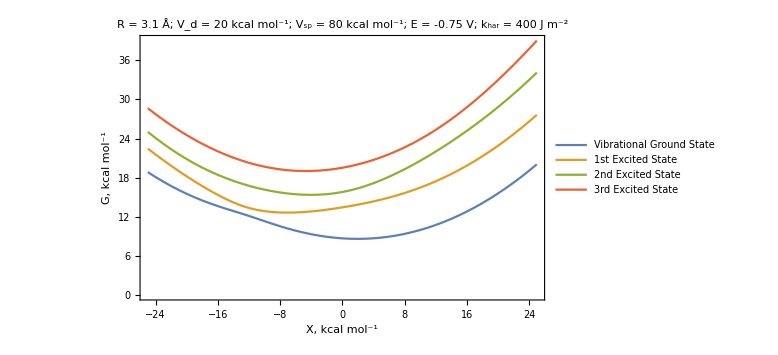

```mathematica
Diag1DFES[20,80,0.62ev2kcal,SHEA,10,TT,xCL,xOHL,εCLA,εw,c0ionsA,1.7,zH3O,400,3.10,-0.75,-90,60,200,0.005,4,Options[{M->mH,DiffOrder->2}]]
```

```mathematica
(* Vibrational ground state and first three excited states at saddle point R *)
```

{{-25.,17.0085},{-24.,16.2724},{-23.,15.5855},{-22.,14.9477},{-21.,14.3589},{-20.,13.8189},{-19.,13.3277},{-18.,12.885},{-17.,12.4908},{-16.,12.1447},{-15.,11.8466},{-14.,11.596},{-13.,11.3923},{-12.,11.2346},{-11.,11.1215},{-10.,11.0498},{-9.,11.0127},{-8.,10.9908},{-7.,10.9294},{-6.,10.7614},{-5.,10.5276},{-4.,10.2912},{-3.,10.0773},{-2.,9.89484},{-1.,9.74791},{0.,9.63854},{1.,9.56803},{2.,9.53727},{3.,9.54692},{4.,9.59751},{5.,9.68949},{6.,9.82324},{7.,9.99911},{8.,10.2174},{9.,10.4784},{10.,10.7823},{11.,11.1294},{12.,11.52},{13.,11.9541},{14.,12.4321},{15.,12.9541},{16.,13.5203},{17.,14.1308},{18.,14.7859},{19.,15.4856},{20.,16.2302},{21.,17.0197},{22.,17.8543},{23.,18.7342},{24.,19.6594},{25.,20.6301}}

{{-25.,21.5734},{-24.,20.784},{-23.,20.0355},{-22.,19.3258},{-21.,18.6523},{-20.,18.0111},{-19.,17.3978},{-18.,16.8068},{-17.,16.2324},{-16.,15.6698},{-15.,15.1168},{-14.,14.574},{-13.,14.045},{-12.,13.5349},{-11.,13.0493},{-10.,12.5951},{-9.,12.1821},{-8.,11.8318},{-7.,11.6005},{-6.,11.5563},{-5.,11.6591},{-4.,11.8456},{-3.,12.0906},{-2.,12.3838},{-1.,12.7195},{0.,13.0927},{1.,13.497},{2.,13.9241},{3.,14.3628},{4.,14.8},{5.,15.2254},{6.,15.6369},{7.,16.0418},{8.,16.4511},{9.,16.8748},{10.,17.3205},{11.,17.7935},{12.,18.2978},{13.,18.8358},{14.,19.4095},{15.,20.0204},{16.,20.6697},{17.,21.3582},{18.,22.0868},{19.,22.8561},{20.,23.6665},{21.,24.5187},{22.,25.413},{23.,26.3498},{24.,27.3295},{25.,28.3523}}

{{-25.,24.5221},{-24.,23.5727},{-23.,22.6592},{-22.,21.7833},{-21.,20.9477},{-20.,20.1561},{-19.,19.4131},{-18.,18.7244},{-17.,18.096},{-16.,17.5326},{-15.,17.0368},{-14.,16.6078},{-13.,16.2422},{-12.,15.9349},{-11.,15.6807},{-10.,15.4747},{-9.,15.3124},{-8.,15.1899},{-7.,15.1037},{-6.,15.051},{-5.,15.0295},{-4.,15.0374},{-3.,15.0743},{-2.,15.1407},{-1.,15.2384},{0.,15.3712},{1.,15.5449},{2.,15.768},{3.,16.0524},{4.,16.4116},{5.,16.8564},{6.,17.3886},{7.,18.0011},{8.,18.6822},{9.,19.4205},{10.,20.2069},{11.,21.0335},{12.,21.8937},{13.,22.7814},{14.,23.6911},{15.,24.6181},{16.,25.5593},{17.,26.5132},{18.,27.4805},{19.,28.4632},{20.,29.4644},{21.,30.4873},{22.,31.5352},{23.,32.611},{24.,33.7172},{25.,34.8559}}

{{-25.,27.4957},{-24.,26.5853},{-23.,25.724},{-22.,24.9116},{-21.,24.1475},{-20.,23.4309},{-19.,22.7611},{-18.,22.1371},{-17.,21.558},{-16.,21.023},{-15.,20.5314},{-14.,20.0827},{-13.,19.6765},{-12.,19.3131},{-11.,18.9926},{-10.,18.7157},{-9.,18.4836},{-8.,18.2974},{-7.,18.1586},{-6.,18.0689},{-5.,18.0297},{-4.,18.042},{-3.,18.1066},{-2.,18.2236},{-1.,18.3922},{0.,18.6114},{1.,18.8796},{2.,19.1948},{3.,19.5553},{4.,19.9591},{5.,20.4047},{6.,20.8909},{7.,21.4169},{8.,21.9826},{9.,22.5887},{10.,23.2365},{11.,23.9283},{12.,24.667},{13.,25.4561},{14.,26.2995},{15.,27.2004},{16.,28.1608},{17.,29.1812},{18.,30.26},{19.,31.394},{20.,32.5791},{21.,33.8105},{22.,35.0836},{23.,36.3942},{24.,37.7385},{25.,39.1132}}

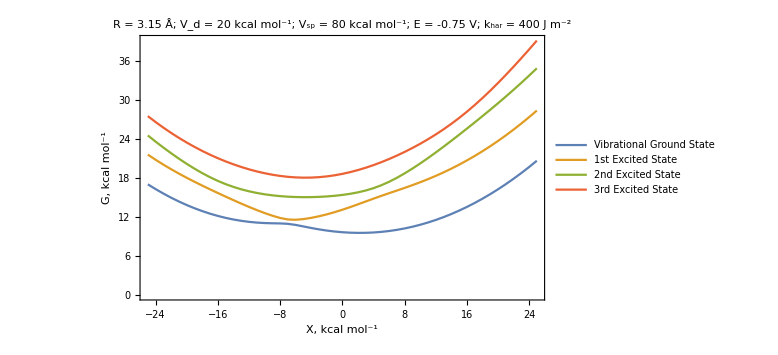

```mathematica
Diag1DFES[20,80,0.62ev2kcal,SHEA,10,TT,xCL,xOHL,εCLA,εw,c0ionsA,1.7,zH3O,400,3.15,-0.75,-90,60,200,0.005,4,Options[{M->mH,DiffOrder->2}]]
```

```mathematica
(* Proton potential at saddle point X and R *)
```

```mathematica
p5=Plot[MorseLeft[0.9380145124719104,DE1A,rp,rDH]+DE1A+8,{rp,0.9,1.3},PlotPoints->100,PlotRange->All,PlotStyle->{Red}];
p6=Plot[MorseRight[0.9004070533563093,DE2A,rp,rAH,3.15]+DE2A+9,{rp,0.9,1.7},PlotPoints->100,PlotRange->All,PlotStyle->{Blue}];
```

```mathematica
pA=Plot[SolGSFixedRQuiet[20,80,0.62ev2kcal,SHEA,-6.5,10,TT,xCL,xOHL,εCLA,εw,c0ionsA,1.7,zH3O,400,3.15,-0.75,-90,60,200,rp],{rp,0.9,1.7},PlotPoints->100,PlotStyle->Purple];
```

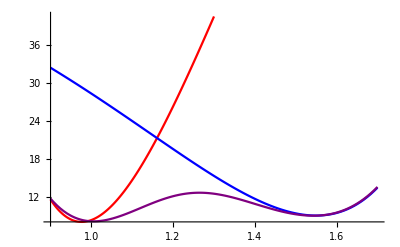

```mathematica
Show[p5,p6,pA]
```

```mathematica
(* Proton potential at saddle point X *)
```

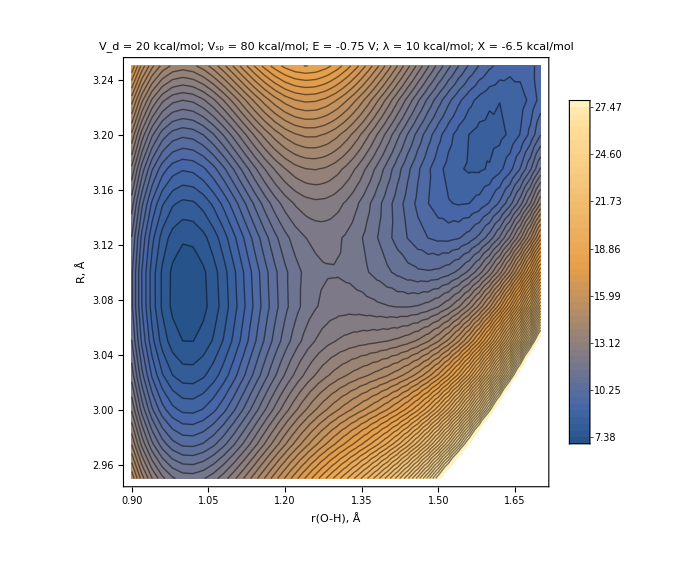

```mathematica
ListContourPlot[Flatten[Table[{rp,R,SolGSFixedRQuiet[20,80,0.62ev2kcal,SHEA,-6.5,10,TT,xCL,xOHL,εCLA,εw,c0ionsA,1.7,zH3O,400,R,-0.75,-90,60,200,rp]},{rp,0.90,1.70,0.02},{R,2.95,3.25,0.025}],1],PlotLegends->Automatic,Contours->50,ImageSize->Large,Frame->True,FrameLabel->{"r(O-H), Å","R, Å"},FrameStyle->Directive[FontFamily->"Helvetica",12,Black],Axes->False,PlotLabel->StringForm["V_d = 20 kcal/mol; V_sp = 80 kcal/mol; E = -0.75 V; λ = 10 kcal/mol; X = -6.5 kcal/mol"],LabelStyle->{FontFamily->"Helvetica",12,GrayLevel[0]}
]
```